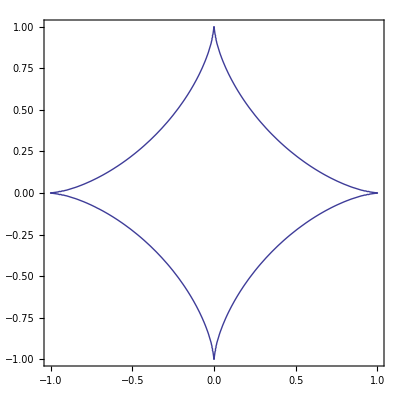

```mathematica
(*Построим график астроиды*)
G=ContourPlot[CubeRoot[x^2]+CubeRoot[y^2]==1,{x,-1,1},{y,-1,1}]
```

Площадь астроиды равна: 1.432

Точное значение площади астроиды равно: (3 π)/8

Погрешность вычислений равна: 0.253903

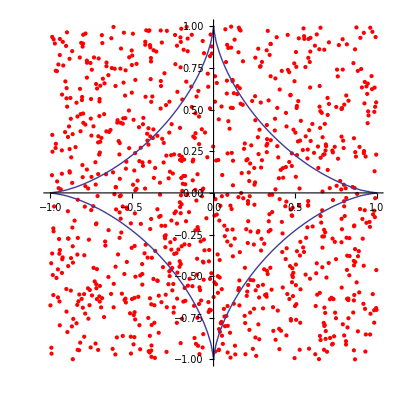

```mathematica
(*Зададим количество точек*)
n=1000;
(*Зададим равномерное распределение в квадрате [-1;1]x[-1;1]*)Points=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{k,1,n}];
(*Найдем площадь астроиды, используя метод Монте-Карло*)
Inside=0;
For[k=1,k≤n,k++,
If[CubeRoot[Points[[k,1]]^2]+CubeRoot[Points[[k,1]]^2]≤1,Inside=Inside+1]
]
S=Inside/n*4;
RV=4*Integrate[Sqrt[(1-x^(2/3))]^3,{x,0,1}];
Print["Площадь астроиды равна: ",N[S]]
Print["Точное значение площади астроиды равно: ",RV]
Print["Погрешность вычислений равна: ",N[Abs[S-RV]]]
(*Выполним графическую иллюстрацию метода Монте-Карло*)
GP=ListPlot[Points,PlotStyle->Red,AspectRatio->Automatic];
Show[GP,G]
```